```mathematica
a[x_] := x
b[x_] := x^2
c[x_] :=x^4
d[x_] := x^8
e[x_] := x^16
f[x_] := x^32
s[x_] := x^100000
g[x_] := If[x==0, 0, 1]
h[x_] := (d[x] + a[x])/2
i[x_] := (e[x] + b[x])/2
j[x_] := (f[x] + c[x])/2
```

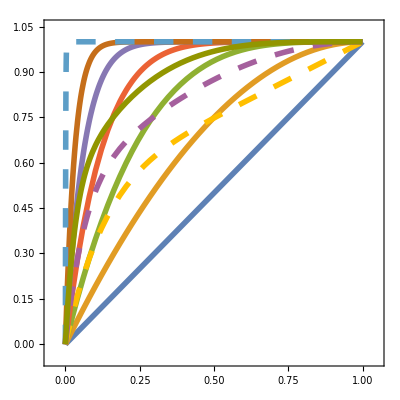

```mathematica
Plot[{ 1-a[1-x],1- b[1-x], 1-c[1-x], 1-d[1-x], 1-e[1-x], 1-f[1-x], 1-s[1-x],1-h[1-x], 1-i[1-x], 1-j[1-x]},{x,0,1},PlotRange->{{-0.05,1.05},{-0.05,1.05}}, AspectRatio->1, Frame->True , PlotStyle->{
Thickness[0.01],
Thickness[0.01],
Thickness[0.01],
Thickness[0.01],
Thickness[0.01],
Thickness[0.01],
Thickness[0.01],
{Thickness[0.01], Dashing[Large]},
{Thickness[0.01], Dashing[Large]},
{Thickness[0.01], Dashing[Large]}
}]
```

```mathematica
Export["CurveDown.pdf",Plot[{ a[1-x], b[1-x], c[1-x], d[1-x], e[1-x], f[1-x], h[1-x], i[1-x], j[1-x]},{x,0,1},PlotRange->{{-0.05,1.05},{-0.05,1.05}}, AspectRatio->1, Frame->True , PlotStyle->{
Thickness[0.01],
Thickness[0.01],
Thickness[0.01],
Thickness[0.01],
Thickness[0.01],
Thickness[0.01],
{Thickness[0.01], Dashing[Large]},
{Thickness[0.01], Dashing[Large]},
{Thickness[0.01], Dashing[Large]}
}]]
```

CurveDown.pdf